Далее в блокноте:
	Ω[β, α] -- частота Раби
	ωR[β, α] -- частота перехода β→α
	ωD -- сдвинутая по Доплеру частота лазера 
	ρ[β, α] -- матричный элемент матрицы плотности
	e -- множество возбужденных состояний
	g -- множество ground состояний
	τ -- время жизни

```mathematica
ClearAll[ρ, α, β, γ, i, j, k, Ω, ωR, ρ0, e, g, τ];
```

```mathematica
g = {1};
e = {2};
nStates = Length@Join[g, e];
```

## Print eq

```mathematica
ClearAll[Eq2Print];
Eq2Print[eq_] := eq /. {
τ -> 1, 
Ω[β_, α_] :>   Subscript["Ω", ToString[β]<>ToString[α]], 
ωR[β_, α_] :> Subscript["ω", ToString[β]<>ToString[α]],
C[β_, α_] :> Subscript["C", ToString[β]<>ToString[α]],
ρ[β_, α_] :> Subscript["ρ", ToString[β]<>ToString[α]],
ωD :> "ω'",
ρRe[β_, α_] :> Subscript["ρ^re", ToString[β]<>ToString[α]],
ρIm[β_, α_] :> Subscript["ρ^im", ToString[β]<>ToString[α]]
};
```

## Релаксационная часть

```mathematica
ClearAll[LPart];
LPart[β_, α_] := -1/(2 τ)ρ0[β, α] /; MemberQ[g, α] && MemberQ[e, β];
LPart[β_, α_] := -1/τ ρ0[β, α]/;α== β && MemberQ[e, β];
LPart[β_, α_] := 1/τ Total@Map[ C[#, α]^2 ρ0[#, #]&, e] /; α == β && MemberQ[g, α];
LPart[β_, α_] := 0;
```

```mathematica
(* пример *)
n = 3;
Table[LPart[i, j], {i, 1, n}, {j, 1, n}] // MatrixForm // FullSimplify // Eq2Print
```

(C_21^2 ρ0[2,2] | 0 | 0
-1/2 ρ0[2,1] | -ρ0[2,2] | 0
0 | 0 | 0)

## Атомарная часть

```mathematica
ClearAll[APart, ωR];
APart[β_, α_] := ℏ (ωR[β, α] - ω) ρ0[β, α] /; β ≠ α;
APart[β_, α_] := ℏ ωR[β, α] ρ0[β, α] /; β == α;
ωR[β_, α_] := 0 /; β == α;
```

```mathematica
(* пример *)
n = 2;
Table[APart[i, j], {i, 1, n}, {j, 1, n}] // MatrixForm // FullSimplify // Eq2Print
```

(0 | ℏ (-ω+ω_12) ρ0[1,2]
ℏ (-ω+ω_21) ρ0[2,1] | 0)

## Взаимодейтвие

```mathematica
ClearAll[IPart, Ω];
IPart[β_, α_] :=Sum[
ℏ Ω[β, j] Cos[φ]ρ0[j, α] - ρ0[β, j] ℏ Ω[j, α] Cos[φ]
,{j, 1, nStates}];
Ω[β_, α_] := 0 /; β== α;
(*Ω[α_, β_] := Ω[β, α] /; MemberQ[g, α] && MemberQ[e, β];*)
Ω[α_, β_] := Ω[β, α] /; α < β;
```

```mathematica
(* пример *)
n = 2;
Eq2Print@EqSimplify@IPart[1,1]
```

2 ⅈ ℏ Cos[φ] Im[ρ_21] Ω_21

## Приближения

Важно помнить, что считаем ρ[β1, β2] и ρ[α1, α2] малыми / не влияюшими на динамику.
Также для упрощения все слагаемые вида ρ[α, β] выразим как Conjugate[ρ[β, α]].

```mathematica
ClearAll[ρ0, ρ];
ρ0[i_, j_] := ρ[i, j]/; MemberQ[e,i]&& MemberQ[g,j];
ρ0[i_, j_] := 0 /; MemberQ[e,i]&& MemberQ[e,j]&& i ≠ j;
ρ0[i_, j_] := 0 /; MemberQ[g,i]&& MemberQ[g,j]&& i ≠ j;
ρ0[i_, j_] := Conjugate[ρ[j, i]]/; MemberQ[g,i]&& MemberQ[e,j];
ρ0[i_, j_] := ρ[i, j]/; i == j;
```

```mathematica
ρ0[1, 1]
ρ0[1, 2]
ρ0[2, 2]
```

ρ[1,1]

Conjugate[ρ[2,1]]

ρ[2,2]

## Всё вместе

```mathematica
ClearAll[Expandρ, globA, Re2Im];
globA = {Ω[x_, y_] ∈ Reals&& C[x_, y_] ∈ Reals && ωD ∈ Reals&& φ ∈ Reals && τ ∈ Reals && τ ≠ 0 && ℏ >0 && t >0 && ρIm[x_, y_] ∈ Reals && ρRe[x_, y_] ∈ Reals && ρIm[x_, x_] == 0 && ωR[x_, y_] ∈ Reals&& ω >0};
Re2Im = # /. {
ρ[a_, b_] - Re[ρ[a_, b_]]->ⅈ Im[ρ[a, b]],
Re[ρ[a_, b_]]-ρ[a_, b_]->-ⅈ Im[ρ[a, b]]
}&;
Expandρ[eq_] := eq/. {ρ[x_, y_]  -> ρRe[x, y] + ⅈ ρIm[x, y]};
EqSimplify[eq_] := FullSimplify[eq, Assumptions->globA] ;
```

```mathematica
ClearAll[MasterEq];
MasterEq[β_,α_] :=FullSimplify[ (APart[β, α]+IPart[β, α]+ⅈ ℏ LPart[β, α])/(ⅈ ℏ), Assumptions->globA, TransformationFunctions->{Automatic,Re2Im}];
```

```mathematica
MasterEq[1, 1]
```

(C[2,1]^2 ρ[2,2])/τ+2 Cos[φ] Im[ρ[2,1]] Ω[2,1]

```mathematica
Eq2Print@MasterEq[1, 1]
```

C_21^2 ρ_22+2 Cos[φ] Im[ρ_21] Ω_21

## Матрица диффура

```mathematica
VarsVec = {ρRe[1,1], ρRe[2,2], ρIm[2, 1], ρRe[2, 1]};
VarsVecI = {{1, 1, 1}, {1, 2, 2},{2, 2,1}, {1, 2, 1}};
VarsVec // Eq2Print
```

{(ρ^re)_11,(ρ^re)_22,(ρ^im)_21,(ρ^re)_21}

```mathematica
EvolMatrix = Table[
Coefficient[
EqSimplify@{Re, Im}⟦VarsVecI⟦i⟧⟦1⟧⟧@Expand@Expandρ@MasterEq[Sequence@@(VarsVecI⟦i⟧⟦2;;3⟧)]
,VarsVec⟦j⟧]
, {i, 1, Length@VarsVecI}, {j, 1, Length@VarsVecI}];
```

```mathematica
(* вид уравнения*)
"∂_t "(VarsVec// MatrixForm )  ==(EvolMatrix // MatrixForm )(VarsVec// MatrixForm ) // Eq2Print
```

∂_t  ((ρ^re)_11
(ρ^re)_22
(ρ^im)_21
(ρ^re)_21)==(0 | C_21^2 | 2 Cos[φ] Ω_21 | 0
0 | -1 | -2 Cos[φ] Ω_21 | 0
-Cos[φ] Ω_21 | Cos[φ] Ω_21 | -1/2 | ω-ω_21
0 | 0 | -ω+ω_21 | -1/2) ((ρ^re)_11
(ρ^re)_22
(ρ^im)_21
(ρ^re)_21)

## Графики

```mathematica
Clear[n1, n2, f1];
c=1;
subs =  {ρRe[1,1] -> n1, ρRe[2,2]-> 1-n1, τ-> 1, φ -> 0, ρIm[2,1]-> f,C[2,1] -> c,Ω[2,1] -> ωr, ωR[2, 1] -> ω+δ};
EM = (EvolMatrix/.subs);
EM// MatrixForm  // Eq2Print
```

(0 | 1 | 2 ωr | 0
0 | -1 | -2 ωr | 0
-ωr | ωr | -1/2 | -δ
0 | 0 | δ | -1/2)

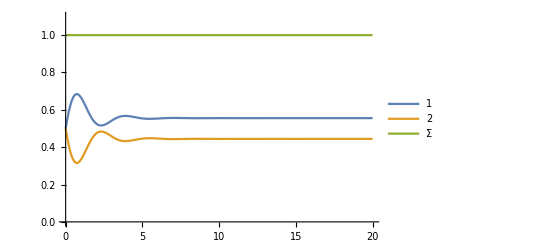
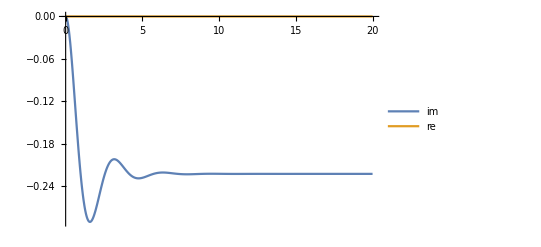
-Graphics- | -Graphics-

```mathematica
vv = {n1[t], n2[t], f1[t], f2[t]};
IC = {n1[0] == 1/2,n2[0] == 1/2,f1[0] == 0, f2[0]== 0};
tMax = 20;
ωr0 =1;
{n1S, n2S, f1S, f2S}=NDSolveValue[D[vv,t] == (EM /. {ωr-> ωr0, φ-> 0, δ-> 0}).vv && IC,vv, {t,0, tMax}];
n1S=n1S⟦0⟧;n2S=n2S⟦0⟧;f1S=f1S⟦0⟧;f2S=f2S⟦0⟧;
Multicolumn[{
Plot[{n1S[t], n2S[t], n1S[t] + n2S[t]}, {t,0, tMax}, PlotRange->{Automatic, {0, 1.1}}, PlotLegends->{1, 2, "Σ"}],
Plot[{f1S[t], f2S[t]}, {t,0, tMax}, PlotRange->Full, PlotLegends->{"im", "re"}]
}]
```

## Резонанс?

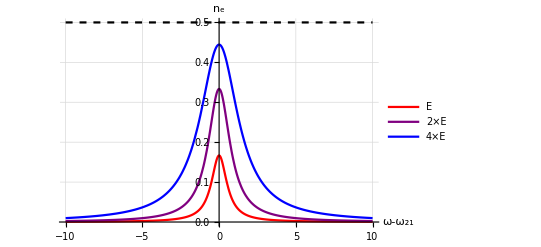

```mathematica
vv = {n1[t], n2[t], f1[t], f2[t]};
IC = {n1[0] == 1, n2[0] == 0,f1[0] == 0, f2[0]== 0};
tMax = 20;
GetA[ωr0_, δ0_] := Module[{n1S, n2S, f1S, f2S},
{n1S, n2S, f1S, f2S}=NDSolveValue[D[vv,t] == (EM /. {ωr-> ωr0, δ-> δ0 }).vv && IC,vv, {t,0, tMax}];
n2S=n2S⟦0⟧;
n2S[tMax]
]
Plot[{GetA[1/4, δ0],GetA[1/2, δ0],GetA[1, δ0], 0.5}, {δ0, -10, 10}, GridLines->Automatic, AxesLabel->{"ω-ω_21","n_e"},PlotLegends->{"E", "2×E", "4×E "}, PlotStyle->{Red, Purple, Blue, {Black, Dashed}}]
```

## Решение

```mathematica
(EvolMatrix.VarsVec)// MatrixForm
```

((C[2,1]^2 ρRe[2,2])/τ+2 Cos[t ωD] ρIm[2,1] Ω[2,1]
-ρRe[2,2]/τ-2 Cos[t ωD] ρIm[2,1] Ω[2,1]
-ρIm[2,1]/(2 τ)-Cos[t ωD] ρRe[1,1] Ω[2,1]+Cos[t ωD] ρRe[2,2] Ω[2,1]+ρRe[2,1] (ω-ωR[2,1])
-ρRe[2,1]/(2 τ)+ρIm[2,1] (-ω+ωR[2,1]))

```mathematica
subsA = {ρRe[1,1] -> n1, ρRe[2,2]->n2, ρIm[2, 1] -> f2, ρRe[2, 1] -> f1,  C[2,1]-> 1, Ω[2,1] -> ωr, ωD -> 0, ω-> ωR[2, 1] + δ};
EM = EvolMatrix /. subsA;
eqsVec = EvolMatrix.VarsVec /. subsA;
FullSimplify@Det@EM
eqsVec// MatrixForm
```

0

(n2/τ+2 f2 ωr
-n2/τ-2 f2 ωr
f1 δ-f2/(2 τ)-n1 ωr+n2 ωr
-f2 δ-f1/(2 τ))

```mathematica
EM // MatrixForm
```

(0 | 1/τ | 2 ωr | 0
0 | -1/τ | -2 ωr | 0
-ωr | ωr | -1/(2 τ) | δ
0 | 0 | -δ | -1/(2 τ))

```mathematica
sol = Solve[eqsVec == {0, 0, 0, 0} && n1 + n2 == 1, {n1, n2, f1, f2}]⟦1⟧
n2AS = n2 /. sol;
```

{n1→1-(4 τ^2 ωr^2)/(1+4 δ^2 τ^2+8 τ^2 ωr^2),n2→(4 τ^2 ωr^2)/(1+4 δ^2 τ^2+8 τ^2 ωr^2),f1→(4 δ τ^2 ωr)/(1+4 δ^2 τ^2+8 τ^2 ωr^2),f2→-(2 τ ωr)/(1+4 δ^2 τ^2+8 τ^2 ωr^2)}

```mathematica
n2AS
```

(4 τ^2 ωr^2)/(1+4 δ^2 τ^2+8 τ^2 ωr^2)

```mathematica
Γ = 1/τ;
σA = (Γ^2/4)/(Γ^2/4+δ^2);
Φ = 4 ωr^2 τ;
(σA  Φ)/(Γ+2 σA  Φ) // FullSimplify
```

(4 τ^2 ωr^2)/(1+4 τ^2 (δ^2+2 ωr^2))